# Homework 5

Name: Eslam Muhammed Ahmed Zenhom

ID: 201700788

## Problem 1

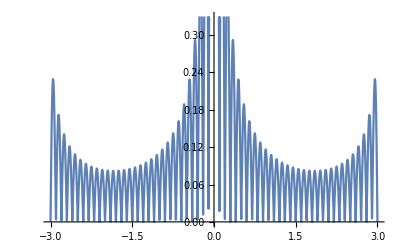

{4.084,{x→2.45952}}

{6.88347,{x→1.43058}}

{31.6228,{x→-2.86039×10^-15}}

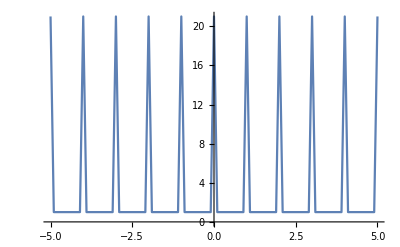

```mathematica
T=10;
dt=0.1;
v=3.2;
s=100;
f[n_]:=Abs[(1/Sqrt[T])*Sum[Exp[-2*π*I*n*((-(T/2)+k*dt)/T)]*(1+Sin[2*π*v*(-T/2+k*dt)])*dt,{k,0,s-1}]];
Plot[ f[ T*x ],{x,-3,3}]
FindMaximum[T f[x],{x,2}]
FindMaximum[T f[x],{x,1}]
FindMaximum[T f[x],{x,0}]
f1[t_]:=(1/Sqrt[T])*Sum[Exp[2*Pi*I*n*t/T]*f[T n],{n,-100,100}];
list={};
Do[AppendTo[list,{t,Abs[f1[t]]}],{t,-T/2,T/2,dt}]
ListPlot[list,Joined-> True,PlotRange->All]
```

## Problem 3

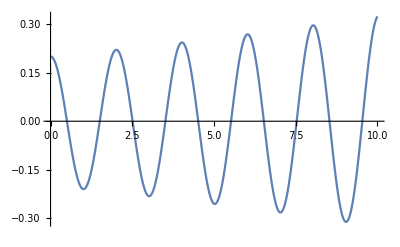

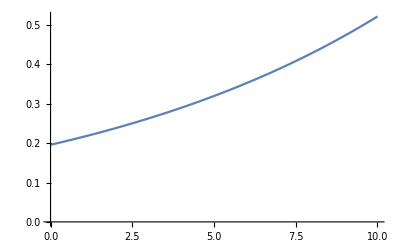

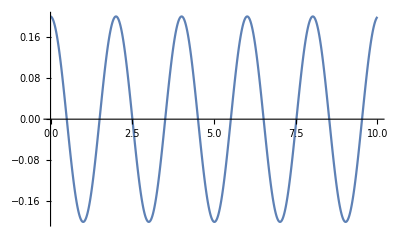

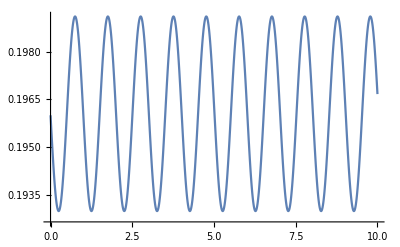

```mathematica
ClearAll["Global`*"];
length = 1.0;
grav = 9.8;
m=1;
dt = 0.01;
ts = 0.0; tend = 10;
tL = Range[ts, tend, dt];
lt = Length[tL];
c=grav/length;
(*First is the euler method*)
theta1 = 0 tL;
omega1 = 0 tL;
energy1=0tL;
theta1[[1]] = 0.2;
omega1[[1]] = 0.0;
energy1[[1]]=0.5*(omega1[[1]]^2+c*theta1[[1]]^2);
(* E=1/2*m*l^2(w^2 + g/l*theta^2) *)
Do[theta1[[i]] = theta1[[i-1]]+omega1[[i-1]] dt; omega1[[i]]=omega1[[i-1]]-c*theta1[[i-1]]*dt; energy1[[i]]=0.5*(omega1[[i]]^2+c*theta1[[i]]^2),{i,2,Length[tL]}];
tth1 = Table[{tL[[j]],theta1[[j]]},{j,lt}];
te1=Table[{tL[[j]],energy1[[j]]},{j,lt}];
ListPlot[tth1, PlotRange->All, Joined->True]
ListPlot[te1, PlotRange->All, Joined->True]





(*Second is the euler cromer method*)
theta2 = 0 tL;
omega2 = 0 tL;
energy2=0tL;
theta2[[1]] = 0.2;
omega2[[1]] = 0.0;
energy2[[1]]=0.5*(omega2[[1]]^2+c*theta2[[1]]^2);
(* E=1/2*m*l^2(w^2 + g/l*theta^2) *)
Do[omega2[[i]]=omega2[[i-1]]-c*theta2[[i-1]]*dt;theta2[[i]] = theta2[[i-1]]+omega2[[i]] dt;  energy2[[i]]=0.5*(omega2[[i]]^2+c*theta2[[i]]^2),{i,2,Length[tL]}];
tth2 = Table[{tL[[j]],theta2[[j]]},{j,lt}];
te2=Table[{tL[[j]],energy2[[j]]},{j,lt}];
ListPlot[tth2, PlotRange->All, Joined->True]
ListPlot[te2, PlotRange->All, Joined->True]

(* The behaviour of the differnce in energy within one cycle:
 as it is obvious from the first two graphs (euler method) that within each cycle the energy increases all the time which makes no sense. Thus, the system for euler method is {{{unstable}}}*)
(*From the third and fourth graph (euler cromer method, It is obvious that in the fourth graph that the energy alternates. However, after each cycle it cames to the same value which makes the energy is same after each peroid T. This make sense from conservation of energy and therefore the system for euler cromer method is {{{stable}}})*)
(*In the attachments on google classroom: you will find a photo for the calcluation of energy in the euler cromer method the minus sign illustrates how the energy became the same after each cycle which doesn't happen in euler method as the minus was a positive sign*)
```

## Problem 2

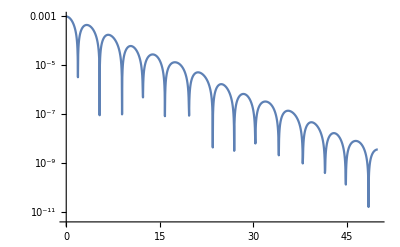

{λ→-172.683}

```mathematica
ClearAll["Global`*"];
length = 9.8;
grav = 9.8;
q=0.5;
dt = 0.04;
ts = 0.0; tend = 50;
tL = Range[ts, tend, dt];
lt = Length[tL];
c=grav/length;
theta1 = 0 tL;
theta2 = 0 tL;
omega1 = 0 tL;
omega2 = 0 tL;
theta1[[1]] = 0.2;
theta2[[1]]=0.2+0.001;
omega1[[1]] = 0.0;
omega2[[1]] = 0.0;
fd=0.5;
omegadri=2/3;

Do[omega1[[i]]=omega1[[i-1]]-(c*Sin[theta1[[i-1]]]+q*omega1[[i-1]]-fd*Sin[omegadri*tL[[i-1]]])*dt;theta1[[i]] = theta1[[i-1]]+omega1[[i]] dt,{i,2,Length[tL]}];


Do[omega2[[i]]=omega2[[i-1]]-(c*Sin[theta2[[i-1]]]+q*omega2[[i-1]]-fd*Sin[omegadri*tL[[i-1]]])*dt;theta2[[i]] = theta2[[i-1]]+omega2[[i]] dt,{i,2,Length[tL]}];


abstheta=0 tL;
Do[abstheta[[i]]=Abs[theta1[[i]] -theta2[[i]] ],{i,1,Length[tL]}]
abst = Table[{tL[[j]],abstheta[[j]]},{j,lt}];
ListLogPlot[abst, PlotRange->All, Joined->True]
FindFit[abst,Exp[λ*t],λ,t]
```

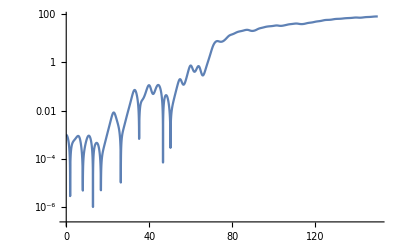

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{λ→0.329769}

```mathematica
(*THE  SECOND PLOT*)
ClearAll["Global`*"];
length = 9.8;
grav = 9.8;
q=0.5;
dt = 0.04;
ts = 0.0; tend = 150;
tL = Range[ts, tend, dt];
lt = Length[tL];
c=grav/length;
theta1 = 0 tL;
theta2 = 0 tL;
omega1 = 0 tL;
omega2 = 0 tL;
theta1[[1]] = 0.2;
theta2[[1]]=0.2+0.001;
omega1[[1]] = 0.0;
omega2[[1]] = 0.0;
fd=1.2;
omegadri=2/3;

Do[omega1[[i]]=omega1[[i-1]]-(c*Sin[theta1[[i-1]]]+q*omega1[[i-1]]-fd*Sin[omegadri*tL[[i]]])*dt;theta1[[i]] = theta1[[i-1]]+omega1[[i]] dt,{i,2,Length[tL]}];


Do[omega2[[i]]=omega2[[i-1]]-(c*Sin[theta2[[i-1]]]+q*omega2[[i-1]]-fd*Sin[omegadri*tL[[i]]])*dt;theta2[[i]] = theta2[[i-1]]+omega2[[i]] dt,{i,2,Length[tL]}];



abstheta=0 tL;
Do[abstheta[[i]]=Abs[theta1[[i]] -theta2[[i]] ],{i,1,Length[tL]}]
abst = Table[{tL[[j]],abstheta[[j]]},{j,lt}];
ListLogPlot[abst, PlotRange->All, Joined->True]
FindFit[abst,Exp[λ*t],λ,t]
```

## Problem 4

```mathematica
ClearAll["Global`*"];
length = 9.8;
grav = 9.8;
q=0.5;
dt = 0.01;
c=grav/length

fd1=1.35;
fd2=1.55;
dfd=0.0005;
Fd=Range[fd1,fd2,dfd];
omegadri=2/3;
drivperoid=2*Pi/omegadri;
sol={};
table={};
Do[a=NDSolveValue[{y''[t]==-c Sin[y[t]]-q y'[t]+Fd[[i]]*Sin[omegadri t],y'[0]=0,y[0]=0.01},y,{t,300*drivperoid,400 *drivperoid}];AppendTo[sol,a],{i,Length[Fd]}];
Do[AppendTo[table,{Fd[[i]],Mod[sol[[i]]*[300*drivperiod+drivperiod*j],Pi]}],{i,Length[Fd]},{j,100}];
ListPlot[table, PlotRange->All, Joined->True]


(*I realy don't know what is the error with this NDSolverValue: I tried it on my friend labtop: hope it will work with you. I tried to find if there is error in the code or not, but I just got tired of that, I think mathematica function of NDSolve  is the problem*)
```

1.

NDSolveValue::deqn: Equation or list of equations expected instead of 0 in the first argument {y''[t]==1.35 Sin[(2 t)/3]-1. Sin[y[t]]-0.5 y'[t],0,0.01}.

NDSolveValue::deqn: Equation or list of equations expected instead of 0 in the first argument {y''[t]==1.3505 Sin[(2 t)/3]-1. Sin[y[t]]-0.5 y'[t],0,0.01}.

General::stop: Further output of NDSolveValue::deqn will be suppressed during this calculation.